```mathematica
Solve[{0==x(4+y-x^2),0==y*(x-1)},{x,y}]
```

{{x→-2,y→0},{x→1,y→-3},{x→2,y→0},{x→0,y→0}}

```mathematica
(*Linearize around (2,0)*)
```

```mathematica
x*(4+y-x^2)/.{x->2+ex,y->0+ey}//Expand
```

-8 ex-6 ex^2-ex^3+2 ey+ex ey

```mathematica
y*(x-1)/.{x->2+ex,y->0+ey}//Expand
```

ey+ex ey

```mathematica
Eigensystem[{{-8,2},{0,1}}]
```

{{-8,1},{{1,0},{2,9}}}

```mathematica
(*Linearize around (-2,0)*)
```

```mathematica
x*(4+y-x^2)/.{x->-2+ex,y->0+ey}//Expand
```

-8 ex+6 ex^2-ex^3-2 ey+ex ey

```mathematica
y*(x-1)/.{x->-2+ex,y->0+ey}//Expand
```

-3 ey+ex ey

```mathematica
Eigensystem[{{-8,-2},{0,-3}}]
```

{{-8,-3},{{1,0},{-2,5}}}

```mathematica
(*Linearize around (0,0)*)
```

```mathematica
x*(4+y-x^2)/.{x->0+ex,y->0+ey}//Expand
```

4 ex-ex^3+ex ey

```mathematica
y*(x-1)/.{x->0+ex,y->0+ey}//Expand
```

-ey+ex ey

```mathematica
Eigensystem[{{4,0},{0,-1}}]
```

{{4,-1},{{1,0},{0,1}}}

```mathematica
(*Linearize around (1,-3)*)
```

```mathematica
x*(4+y-x^2)/.{x->1+ex,y->-3+ey}//Expand
```

-2 ex-3 ex^2-ex^3+ey+ex ey

```mathematica
y*(x-1)/.{x->1+ex,y->-3+ey}//Expand
```

-3 ex+ex ey

```mathematica
Eigensystem[{{-2,1},{0,-3}}]
```

{{-3,-2},{{-1,1},{1,0}}}

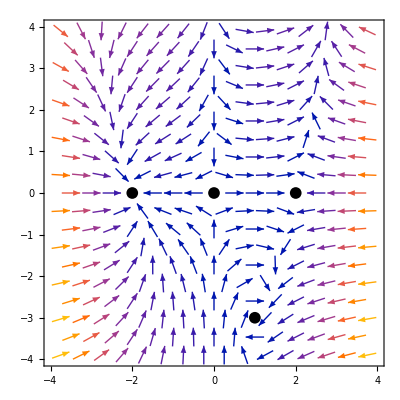
-Graphics-yx

```mathematica
Labeled[Show[VectorPlot[{x(4+y-x^2),y(x-1)},{x,-4,4},{y,-4,4}],
ListPlot[{{0,0},{2,0},{-2,0},{1,-3}},PlotMarkers->{Automatic,12},PlotStyle->{Thick,Black}]],{"y","x"},{Left,Bottom}]
```